# Impact of Urban Design on Quality of Life

## Intro

Most of the population around the globe is now concentrated in cities. There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.
This work is a stepping stone in that direction.

## What is quality of life?

This is a very non-trivial question and we are not going to answer it in this work. Instead we will define a very simple approximation of quality of life as average sentiment across Tweets related to that specific city.

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
EstimateQualityOfLifeWSentiment[data_] := Module[{tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	data = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[data];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	{meanPositivness, meanCertainty}
];
RescaleIntoInterval[numbers_List, numberNewSmallest_, numberNewLargest_] := Map[(# * (numberNewLargest - numberNewSmallest) + numberNewSmallest) &, Rescale[numbers]];
RescaleIntoInterval[numbers_List] := RescaleIntoInterval[numbers, 0.5, 0.95];
```

## Which regions are we going to analyze?

rer

```mathematica
constantDirectory = "/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts";
constantPathTweets = StringJoin[{constantDirectory, "/Tweets"}];
constantPathFeatures = StringJoin[{constantDirectory, "/Features"}];
constantPathMaps = StringJoin[{constantDirectory, "/Maps"}];
constantCityDiameterKM = 10;
constantCityGridSize = 5;
(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
CityRowParse[cityRow_List] := { Interpreter["City"][StringJoin[cityRow⟦2⟧, ", ", cityRow⟦3⟧]], cityRow⟦1⟧ };
citiesWRanks = Map[CityRowParse, Drop[Import["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/Inputs/CitiesMercer2019.csv"], 1]];
citiesPopular = citiesWRanks[[All, 1]];

CityName[city_] := EntityValue[city, "Name"];
CityDataPath[directory_String, city_String] := StringJoin[{directory, "/", city, ".mx"}];
CityDataPath[directory_String, city_] := CityDataPath[directory, CityName[city]];
```

Lets collect Twitter data.

```mathematica
tw = ServiceConnect["Twitter"];
ExtractTweets[city_] := Normal[tw["TweetSearch", "Query"->CityName[city]]];
ExportTweets[city_] := Export[CityDataPath[constantPathTweets, city],ExtractTweets[city]];
ImportTweets[city_] := Import[CityDataPath[constantPathTweets, city]];
```

Once we collect the data from Twitter, we want to see how the

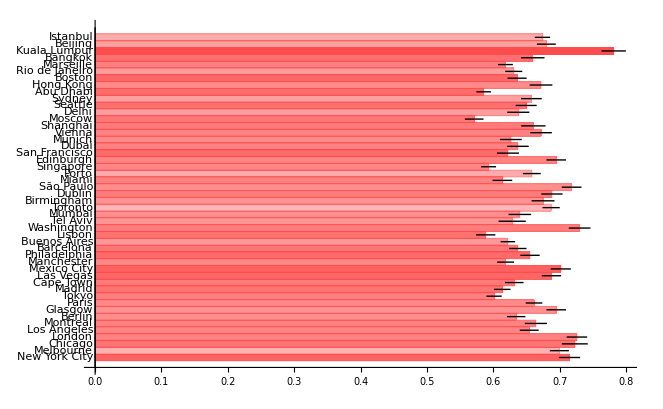

```mathematica
citiesEstimates = Map[TwEstimateQualityOfLife, citiesPopular];
citiesCertainties = RescaleIntoInterval[Map[(#["Value"]) &, citiesEstimates⟦All, 2⟧]];
citiesColors = Map[RGBColor[1, 0.3, 0.3, #] &, citiesCertainties];
citiesPositivness = citiesEstimates⟦All, 1⟧;
BarChart[citiesPositivness,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

As we can see, there is not much variance between cities, in terms of Tweets sentiment.
Lets compile multiple rankings together, assuming that they have had a more complete model for estimating the quality of life and satisfaction.

```mathematica
citiesPositivness = RescaleIntoInterval[Map[(N[1/#])&, citiesWRanks⟦All, 2⟧]];
```

## Are there any correlations at all?

wew

```mathematica
ExtractMaps[city_] := Module[{cityBounds, gridLats, gridLons, cityParts, cityImages, MakeCell, ImageForCell},
	cityBounds = Normal[GeoBoundingBox[GeoPosition[city], Quantity[constantCityDiameterKM, "Kilometers"]]];
	gridLats = Subdivide[Latitude[cityBounds⟦1⟧],Latitude[cityBounds⟦2⟧], constantCityGridSize+1];
	gridLons = Subdivide[Longitude[cityBounds⟦1⟧],Longitude[cityBounds⟦2⟧], constantCityGridSize+1];
	MakeCell[i_Integer, j_Integer] := GeoRange[{gridLats⟦i⟧, gridLats⟦i+1⟧}, {gridLons⟦j⟧, gridLons⟦j+1⟧}];
	cityParts = Flatten[Table[MakeCell[i, j], {i, constantCityGridSize}, {j, constantCityGridSize}]];
	ImageForCell[coords_] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[GeoRange->coordsAsList]]
	];
	cityImages = Map[ImageForCell, cityParts]
];
ExportMaps[city_] := Export[CityDataPath[constantPathMaps, city],ExtractMaps[city]];
ImportMaps[city_] := Import[CityDataPath[constantPathMaps, city]];
```

```mathematica
ExtractListFeatures[object_, props_List] := Normal[Map[({#, Normal[object[#]]}) &, props]];
ExtractCityStatsFeatures[city_] := Module[{props}, 
	props = {"Population","Latitude","Longitude","Elevation","MagneticFieldStrength"};
	ExtractListFeatures[city, props]
];
ExtractCountryStatsFeatures[city_] := Module[{props, country},
	country = city["Country"];
	props = {"Population","Latitude","Longitude",
	"Area","WaterArea","BoundaryLength",
	"ChildPopulation","ContributingFamilyWorkers","ElderlyPopulation","HIVAIDSPopulation",
	"NetIncomeFromAbroad","GovernmentDebt","GovernmentSurplus","ImportsValue","ExportsValue",
	"GiniIndex","Army"};
	ExtractListFeatures[country, props]
];
ExtractMapFeatures[city_] := Module[{},
	List[]
];
ExtractAllFeatures[city_] := Join[ExtractCityStatsFeatures[city], ExtractCountryStatsFeatures[city], ExtractMapFeatures[city]];
ExportAllFeatures[city_] := Export[CityDataPath[constantPathFeatures, city], ExtractAllFeatures[city]];
ImportAllFeatures[city_] := Import[CityDataPath[constantPathFeatures, city]];
```

```mathematica
NormalizeFeatures[rowsPerSample_List] := Module[{rowsPerFeature, rowsPerFeatureNormalized},
	rowsPerFeature = Transpose[rowsPerSample];
	rowsPerFeatureNormalized = Map[(RescaleIntoInterval[Rescale[#], 0.5, 1]) &, rowsPerFeature];
	Transpose[rowsPerFeatureNormalized]
];
RunRegression[rowsPerSample_, predictionsVals_] := Module[{inputNormalized, p, pLinearLayer, pWeights},
	inputNormalized = NormalizeFeatures[rowsPerSample];
	p = Predict[rowsPerSample->predictionsVals, Method->"LinearRegression"];
	pLinearLayer = p⟦1, "Model", "MeanFunction"⟧;
	pWeights = Normal @ pLinearLayer⟦"Arrays"⟧⟦"Weights"⟧;
	{p, pWeights}
];
RunLinear[rowsPerSample_, estimatesPerSample_, featuresNames_List, trainingCount_Integer] := Module[{inputTrain, inputValidate, outputTrain, outputValidate, outputEstimated, modelData, error, chart, result},
	inputTrain = Take[rowsPerSample, trainingCount];
	inputValidate = Drop[rowsPerSample, trainingCount];
	outputTrain = Take[estimatesPerSample, trainingCount];
	outputValidate = Drop[estimatesPerSample, trainingCount];
	modelData = RunRegression[inputTrain, outputTrain];
	outputEstimated = Map[modelData⟦1⟧, inputValidate];
	error = Norm[outputValidate-outputEstimated, 1] / Length[outputValidate];
	chart = BarChart[modelData⟦2⟧, ChartLabels->featuresNames, BarOrigin->Left];
	Echo[Length[outputEstimated]];
	Echo[ScientificForm[modelData⟦2⟧]];
	{error, chart, modelData}
];
```

```mathematica
citiesFeatures = Map[ImportAllFeatures[#] &, citiesPopular];
citiesFeaturesValues = Map[Apply[Normal, #, {1, 2}] &, citiesFeatures⟦All, All, 2⟧]; (*Transform units into raw numbers.*)
citiesFeaturesNames = First[citiesFeatures⟦All, All, 1⟧];
```

```mathematica
ClearSystemCache[]
```

15

{{-1.04754×10^-5,-1.54378×10^-6,-6.74951×10^-6,-6.51852×10^-6,-1.49768×10^-6,-1.28781×10^-6,-5.14644×10^-6,-1.15958×10^-5,8.95465×10^-6,-1.45947×10^-5,1.33416×10^-5,8.19344×10^-6,1.4518×10^-5,-7.03844×10^-6,2.42923×10^-5,-1.53608×10^-7,1.0828×10^-5,1.85765×10^-6,1.79305×10^-6,-3.81617×10^-6,-4.62132×10^-6,2.34534×10^-6,-2.39964×10^-6,3.76315×10^-6,6.40306×10^-7,-4.97856×10^-7,-6.20755×10^-6,1.08298×10^-5,3.55284×10^-6,1.34271×10^-5,-2.34937×10^-6,-1.52242×10^-5,2.8545×10^-6,1.29987×10^-7,2.39972×10^-5,1.66787×10^-6,2.27739×10^-5,1.70638×10^-6,-9.08597×10^-6,-7.35048×10^-6,2.82437×10^-6,3.47061×10^-6,1.19218×10^-5,7.56317×10^-6,-1.63863×10^-5,2.88053×10^-6,4.26353×10^-6,-9.95425×10^-6,-9.32946×10^-6,2.67825×10^-6,-1.63524×10^-5,-1.68321×10^-5,1.63274×10^-5,-1.30446×10^-5,-1.1217×10^-5}}

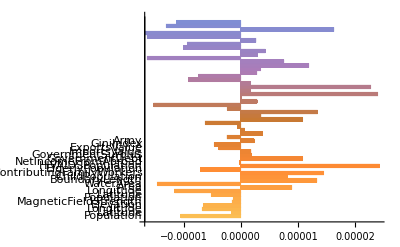

```mathematica
m = RunLinear[citiesFeaturesValues, citiesPositivness, citiesFeaturesNames, 85];
m[[2]]
```

```mathematica
m[[3, 1]][[1]]
```

<|ExampleNumber→85,Input→<|Preprocessor→ToMLDataset,Processor→  ToVector
ToVector→ImputeMissing
ImputeMissing→LogRescaleNumericalVector→Standardize→EmbedNominalVector→MergeVectors|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→Standardize→FromVector→FirstValues,ProbabilityPostprocessor→Identity,InverseProcessorFunction→(0.523603+0.0589424 #1&),ProcessorFunction→(-8.88329+16.9657 #1&),Name→value,Quantiles→{-0.386828,7.23413}|>,Prior→Automatic,Utility→(DiracDelta[#2-#1]&),Threshold→0,PerformanceGoal→Automatic,BatchProcessing→Automatic,Model→<|MeanFunction→LinearLayer[<>],DistributionData→{NormalDistribution,1.71191},Processor→  Standardize→FirstValues,Method→LinearRegression,PostProcessor→Identity,Options→<|L1Regularization→<|Value→0,Options→<||>|>,L2Regularization→<|Value→1.×10^6,Options→<||>|>,OptimizationMethod→<|Value→NormalEquation,Options→<||>|>,MaxIterations→<|Value→30,Options→<||>|>|>|>,TrainingInformation→<|PanelCell→631345,TrainingFunction→Predict,EMIterations→Missing[KeyAbsent,EMIterations],ProcessorEntropyShift→-2.83119,PreprocessingTime→0.15087,LossName→StandardDeviation,BestModelInformation→Dataset[<>],Configurations→Dataset[<>],MaxTrainingSize→85,PreprocessorEvaluationTime→3.761×10^-6,PreprocessorMemory→145792,InputDimension→55,OutputDimension→1,BaselineLogProbability→-1.41894,VariableBudget→True,CheckpointingInfo→<|Checkpointing→False|>,UserStop→False,NaturalStop→True,AbortStop→False,LastReportingTime→3.771344978457821×10^9,RoundPartitioning→Dataset[<>]|>,Log→<|Example→ | Type | Weight | Values
f1 | Numerical | 1 | { 287200. }
f2 | Numerical | 1 | { 0.8039 }
f3 | Numerical | 1 | { 0.2532 }
f4 | Numerical | 1 | { 977.7 }
f5 | Numerical | 1 | { 48.14 }
f6 | Numerical | 1 | { 2.08×10^6 }
f7 | Numerical | 1 | { 0.8049 }
f8 | Numerical | 1 | { 0.2586 }
f9 | Numerical | 1 | { 7827. }
f10 | Numerical | 1 | { 47.1 }
f11 | Numerical | 1 | { 703.8 }
f12 | Numerical | 1 | { 306000. }
f13 | Nominal | 1 | { 25280. }
f14 | Numerical | 1 | { 382200. }
f15 | Nominal | 1 | { 280. }
f16 | Nominal | 1 | { -8.766×10^8 }
⋮_6 |  |  | 
1 examples | no weights | grouped examples | no density weights |  |  | Dataset[Association[(_String -> _Association)..]],TrainingTime→1.11126,MaxTrainingMemory→905144,DataMemory→56824,FunctionMemory→358496,LanguageVersion→{12.,0},Date→Fri 5 Jul 2019 19:49:38GMT-4.,ProcessorCount→4,ProcessorType→x86-64,OperatingSystem→MacOSX,SystemWordLength→64,Evaluations→{}|>|>

## Are there correlations between cities topology and quality of life?

wewe

## Are there correlations between known features and quality of life?

wewe